```mathematica
(*I used getKVec and TofVVec routines from T.nb for the illustration below*)
```

```mathematica
WeigthsTest[knum_]:=Table[1,{n,1,knum}];
weights=WeigthsTest[100];
```

```mathematica
(*temp_ is k_B T in units of energy*)
```

```mathematica
CostTemp[temp_,T_, TGoal_, weights_]:=
Module[{cost},
(*Calculate the cost function*)
cost = Sum[weights[[i]]*(Exp[-T[[i,1]]^2/(2*temp)]/(√(2 temp Pi))T[[i,2]]^2-TGoal[[i,2]])^2,{i,1,Length[T]}] ;
Return[cost];
];
```

```mathematica
TGoalTest=Table[{x,Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2)Exp[-x^2/(2)]/(√(2 Pi))},{x,kVecTest}];(* here temp=1*)
```

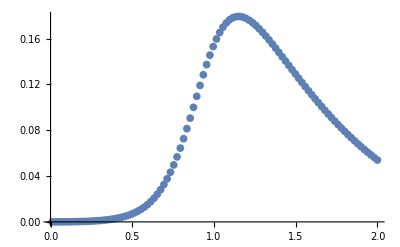

```mathematica
ListPlot[TGoalTest]
```

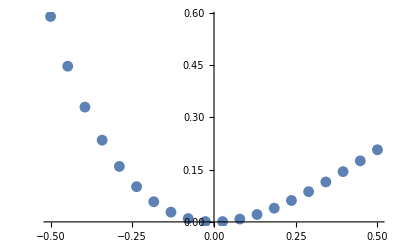

```mathematica
ListPlot[Table[{eps,CostTemp[1,Abs[TofVVec[VTest,{1+eps,0,1},SEDict,kVecTest]],TGoalTest,weights]},{eps,-0.5,0.5,1/19}]]
```